```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
(*accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/EVBK/gdc_VER_EVBK_points.txt"];*)
accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/POINTS/gdc_VER_EVBK_points.txt"];
accCH=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/CH/gdc_VER_CH_points.txt"];
confMaxTat100=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_MAX/MAX_TAT_1_00.txt"];
confMaxTat101=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_MAX/MAX_TAT_1_01.txt"];
confMaxTat105=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_MAX/MAX_TAT_1_05.txt"];
names=Keys[accEVBK]
confs={"DOJ","Z","F"};
timesteps=Range[17];
col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]]
(*col1=Map[ColorData["BlueGreenYellow"][#]&,Range[Length[timesteps]]/Length[timesteps]]
col3=Map[Hue[#]&,Range[Length[timesteps]]/Length[timesteps]]
col4=Map[Hue[1,#]&,Range[Length[timesteps]]/Length[timesteps]]
col5=Map[ColorData["TemperatureMap"][#]&,Range[Length[timesteps]]/Length[timesteps]]*)
homeAdd="/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/";
spezAdd="CONF_MAX/RAT_1_01/";
plotType="MAX";
revType="ALL";
```

{DLB,MUR,LYE,PHI,SED,AUS}

{RGBColor[Rational[1, 17], Rational[1, 17], Rational[16, 17]],RGBColor[Rational[2, 17], Rational[2, 17], Rational[15, 17]],RGBColor[Rational[3, 17], Rational[3, 17], Rational[14, 17]],RGBColor[Rational[4, 17], Rational[4, 17], Rational[13, 17]],RGBColor[Rational[5, 17], Rational[5, 17], Rational[12, 17]],RGBColor[Rational[6, 17], Rational[6, 17], Rational[11, 17]],RGBColor[Rational[7, 17], Rational[7, 17], Rational[10, 17]],RGBColor[Rational[8, 17], Rational[8, 17], Rational[9, 17]],RGBColor[Rational[9, 17], Rational[9, 17], Rational[8, 17]],RGBColor[Rational[10, 17], Rational[10, 17], Rational[7, 17]],RGBColor[Rational[11, 17], Rational[11, 17], Rational[6, 17]],RGBColor[Rational[12, 17], Rational[12, 17], Rational[5, 17]],RGBColor[Rational[13, 17], Rational[13, 17], Rational[4, 17]],RGBColor[Rational[14, 17], Rational[14, 17], Rational[3, 17]],RGBColor[Rational[15, 17], Rational[15, 17], Rational[2, 17]],RGBColor[Rational[16, 17], Rational[16, 17], Rational[1, 17]],RGBColor[1, 1, 0]}

```mathematica
(* Ratio > 1.01 *)
dataDOJ=sumUpFunc[accEVBK, accCH,confMaxTat101,"DOJ",names,revType];
dataZ=sumUpFunc[accEVBK, accCH,confMaxTat101,"Z",names,revType];
dataF=sumUpFunc[accEVBK, accCH,confMaxTat101,"F",names,revType];
```

```mathematica
shrinkFac1=0.02;
shrinkFac2=0.02;
plotsDOJ=Map[singlePlot[#, dataDOJ,col2,shrinkFac1,shrinkFac2,plotType]&,names];
gridDOJ=Grid[{plotsDOJ[[1;;2]],plotsDOJ[[3;;4]],plotsDOJ[[5;;6]]}];
plotsZ=Map[singlePlot[#, dataZ,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridZ=Grid[{plotsZ[[1;;2]],plotsZ[[3;;4]],plotsZ[[5;;6]]}];
plotsF=Map[singlePlot[#, dataF,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridF=Grid[{plotsF[[1;;2]],plotsF[[3;;4]],plotsF[[5;;6]]}];
```

size {0.109939}

size {0.147939,0.147939,0.147939,0.147939,0.134076}

size {0.147939,0.147939,0.147939,0.147939,0.112103,0.112103,0.112103,0.134076,0.112103,0.147939}

size {0.10635,0.10635,0.112103,0.112103,0.109939}

size {0.112103,0.112103,0.112103,0.112103,0.112103,0.112103,0.112103,0.112103}

size {}

size {0.0240457,0.0252211,0.0456156,0.111193,0.0473607,0.0481312}

size {0.147973,0.147888,0.147888,0.147843,0.134138,0.0348049,0.0512625}

size {0.147973,0.144456,0.144456,0.145197,0.112337,0.112178,0.112167,0.134438,0.11212,0.148088}

size {0.0982498,0.0982494,0.112737,0.112775,0.109865}

size {0.112347,0.112181,0.112181,0.112124,0.112124,0.112114,0.112114,0.112114}

size {}

size {0.0372374,0.0383813,0.0588701,0.0602738,0.0607941,0.0617606,0.0450965,0.0714947}

size {0.0482996,0.0648404}

size {0.0223893,0.0397336,0.0403854}

size {0.0425347,0.0436814}

size {0.0231942}

size {0.0318896}

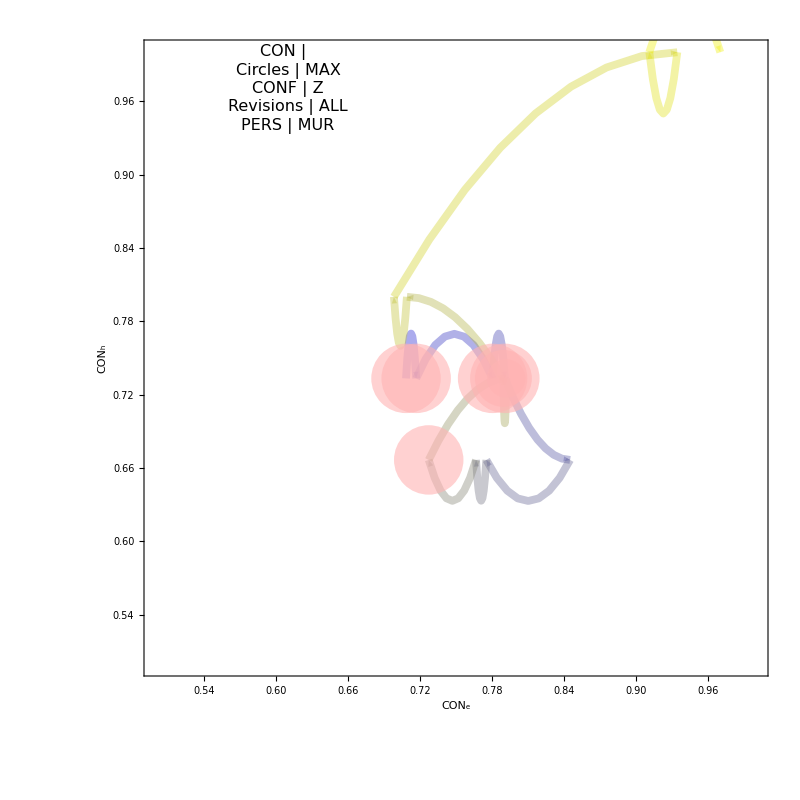
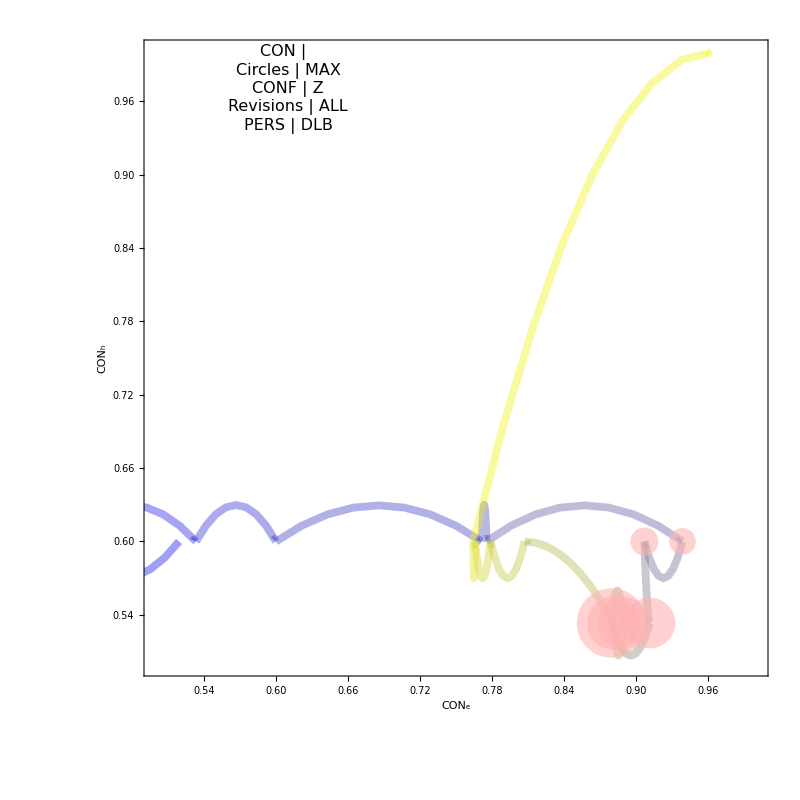

```mathematica
{plotsZ[[2]],plotsZ[[1]]}
```

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType]
Export[ToString[plotType]<>"_DOJ.jpeg",gridDOJ]
Export[ToString[plotType]<>"_Z.jpeg",gridZ]
Export[ToString[plotType]<>"_F.jpeg",gridF]
```

/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_MAX/RAT_1_01/ALL

MAX_DOJ.jpeg

MAX_Z.jpeg

MAX_F.jpeg